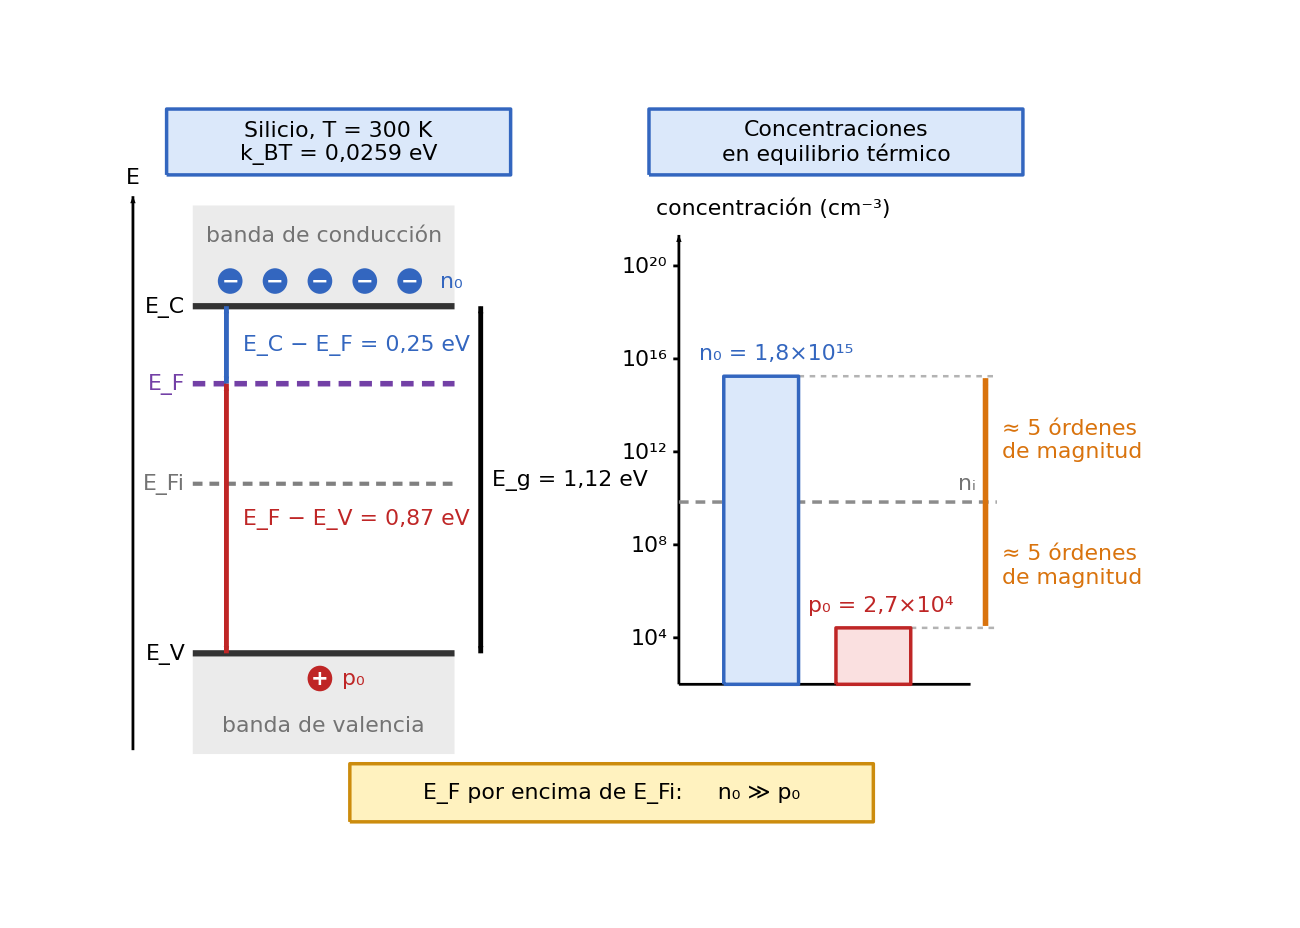

```mathematica
diagramaFermiConc=Module[{fs,mostrarValores,cAzul,cAzulB,cRojo,cRojoF,cVio,cNar,cGris,cOro,cOroB,kT,Nc,Nv,Eg,dCF,dFV,n0,p0,ni,dCi,ordN,ordP,se,yV,yC,yF,yI,px,wb,ox,y0,sy,YL,xb1,xb2,xa,hw,ins,insI,insD,flecha,caja,carga,cota,dec,cient,val},(*----------Parámetros globales----------*)fs=22;(*tamaño de fuente único para todo el gráfico*)mostrarValores=True;(*False oculta los valores numéricos*)cAzul=RGBColor[0.86,0.91,0.98];cAzulB=RGBColor[0.20,0.40,0.75];
cRojo=RGBColor[0.75,0.15,0.15];cRojoF=RGBColor[0.98,0.88,0.88];
cVio=RGBColor[0.45,0.25,0.65];cNar=RGBColor[0.85,0.45,0.05];
cGris=GrayLevel[0.45];
cOro=RGBColor[1.0,0.95,0.75];cOroB=RGBColor[0.80,0.55,0.05];
(*----------Datos del ejemplo (eV,cm^-3)----------*)kT=0.0259;Nc=2.8*10.^19;Nv=1.04*10.^19;Eg=1.12;dCF=0.25;
dFV=Eg-dCF;(*E_F-E_V*)n0=Nc Exp[-dCF/kT];p0=Nv Exp[-dFV/kT];
ni=Sqrt[n0 p0];(*n_i coherente con N_c,N_v y E_g*)dCi=kT Log[Nc/ni];(*E_C-E_Fi*)ordN=Round[Log10[n0/ni]];ordP=Round[Log10[ni/p0]];
(*----------Geometría----------*)se=8.;yV=3.0;yC=yV+se Eg;yF=yC-se dCF;yI=yC-se dCi;
px=2.4;wb=7.0;(*diagrama de bandas*)ox=15.4;y0=2.2;sy=0.6;(*gráfico logarítmico:0,6 unidades por década*)xb1=ox+2.2;xb2=ox+5.2;xa=ox+8.2;hw=1.0;
YL[c_]:=y0+sy (Log10[c]-2);
(*----------Funciones auxiliares----------*)ins[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos];
insI[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos,{Left,Center}];
insD[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos,{Right,Center}];
flecha[p1_,p2_,col_]:={col,AbsoluteThickness[4],Arrowheads[0.02],Arrow[{p1,p2}]};
caja[{xc_,yc_},{w_,h_},relleno_,borde_]:={EdgeForm[{AbsoluteThickness[2.5],borde}],relleno,Rectangle[{xc-w/2,yc-h/2},{xc+w/2,yc+h/2},RoundingRadius->0.15]};
carga[pos_,signo_,col_]:={col,Disk[pos,0.33],Text[Style[signo,Round[0.95 fs],Bold,White],pos]};
cota[x_,y1_,y2_,col_]:={col,AbsoluteThickness[3.5],Arrowheads[{-0.014,0.014}],Arrow[{{x,y1},{x,y2}}]};
dec[x_,k_]:=NumberForm[x,{5,k},NumberPoint->","];
cient[x_]:=Module[{ex=Floor[Log10[x]],m},m=Round[x/10.^ex,0.1];
Row[{NumberForm[m,{2,1},NumberPoint->","],"×",Superscript["10",ex]}]];
val[x_]:=If[mostrarValores,Row[{" = ",cient[x]}],""];
(*----------Diagrama----------*)Graphics[{(*cabeceras*)caja[{6.3,16.2},{9.2,1.7},cAzul,cAzulB],ins[Column[{"Silicio, T = 300 K",If[mostrarValores,Row[{Subscript["k","B"],"T = ",dec[kT,4]," eV"}],""]},Center],{6.3,16.2}],caja[{ox+4.2,16.2},{10.0,1.7},cAzul,cAzulB],ins[Column[{"Concentraciones","en equilibrio térmico"},Center],{ox+4.2,16.2}],(* =====Panel izquierdo:bandas de energía=====*){Black,AbsoluteThickness[2],Arrowheads[0.02],Arrow[{{0.8,0.5},{0.8,14.8}}]},ins[Style["E",Italic],{0.8,15.3}],{GrayLevel[0.92],EdgeForm[None],Rectangle[{px,yC},{px+wb,yC+2.6}],Rectangle[{px,yV-2.6},{px+wb,yV}]},{GrayLevel[0.2],AbsoluteThickness[4.5],Line[{{px,yC},{px+wb,yC}}],Line[{{px,yV},{px+wb,yV}}]},ins["banda de conducción",{px+wb/2,yC+1.85},cGris],ins["banda de valencia",{px+wb/2,yV-1.85},cGris],(*nivel intrínseco y nivel de Fermi*){GrayLevel[0.5],AbsoluteThickness[3],AbsoluteDashing[{7,5}],Line[{{px,yI},{px+wb,yI}}]},{cVio,AbsoluteThickness[4],AbsoluteDashing[{9,6}],Line[{{px,yF},{px+wb,yF}}]},insD[Row[{Subscript["E","C"]}],{px-0.2,yC}],insD[Row[{Subscript["E","F"]}],{px-0.2,yF},cVio],insD[Row[{Subscript["E","Fi"]}],{px-0.2,yI},cGris],insD[Row[{Subscript["E","V"]}],{px-0.2,yV}],(*distancias del nivel de Fermi a los bordes de banda*)cota[px+0.9,yF,yC,cAzulB],insI[Row[{Subscript["E","C"]," − ",Subscript["E","F"],If[mostrarValores,Row[{" = ",dec[dCF,2]," eV"}],""]}],{px+1.35,(yC+yF)/2},cAzulB],cota[px+0.9,yV,yF,cRojo],insI[Row[{Subscript["E","F"]," − ",Subscript["E","V"],If[mostrarValores,Row[{" = ",dec[dFV,2]," eV"}],""]}],{px+1.35,(yV+yF)/2},cRojo],(*banda prohibida*)cota[px+wb+0.7,yV,yC,Black],insI[Row[{Subscript["E","g"],If[mostrarValores,Row[{" = ",dec[Eg,2]," eV"}],""]}],{px+wb+1.0,(yV+yC)/2}],(*portadores:muchos electrones,un hueco*)Table[carga[{px+dx,yC+0.65},"−",cAzulB],{dx,{1.0,2.2,3.4,4.6,5.8}}],insI[Row[{Subscript["n","0"]}],{px+6.6,yC+0.65},cAzulB],carga[{px+3.4,yV-0.65},"+",cRojo],insI[Row[{Subscript["p","0"]}],{px+4.0,yV-0.65},cRojo],(* =====Panel derecho:concentraciones (escala logarítmica)=====*){Black,AbsoluteThickness[2],Arrowheads[0.02],Arrow[{{ox,y0},{ox,13.8}}]},{Black,AbsoluteThickness[2],Line[{{ox,y0},{xa-0.4,y0}}]},insI[Row[{"concentración (",Superscript["cm","−3"],")"}],{ox-0.6,14.5}],Table[{Black,AbsoluteThickness[2],Line[{{ox-0.15,YL[10.^k]},{ox,YL[10.^k]}}],insD[Row[{Superscript["10",k]}],{ox-0.3,YL[10.^k]}]},{k,{4,8,12,16,20}}],(*guías de nivel y distancia a n_i*){GrayLevel[0.55],AbsoluteThickness[2.5],AbsoluteDashing[{7,5}],Line[{{ox,YL[ni]},{xa+0.3,YL[ni]}}]},{GrayLevel[0.7],AbsoluteThickness[1.8],AbsoluteDashing[{4,4}],Line[{{xb1+hw,YL[n0]},{xa+0.3,YL[n0]}}],Line[{{xb2+hw,YL[p0]},{xa+0.3,YL[p0]}}]},ins[Row[{Subscript["n","i"]}],{xb2+2.5,YL[ni]+0.5},cGris],(*barras de n_0 y p_0*){EdgeForm[{AbsoluteThickness[2.5],cAzulB}],cAzul,Rectangle[{xb1-hw,y0},{xb1+hw,YL[n0]}]},{EdgeForm[{AbsoluteThickness[2.5],cRojo}],cRojoF,Rectangle[{xb2-hw,y0},{xb2+hw,YL[p0]}]},ins[Row[{Subscript["n","0"],val[n0]}],{xb1+0.4,YL[n0]+0.6},cAzulB],ins[Row[{Subscript["p","0"],val[p0]}],{xb2+0.2,YL[p0]+0.6},cRojo],(*órdenes de magnitud respecto a n_i*)flecha[{xa,YL[ni]},{xa,YL[n0]-0.05},cNar],flecha[{xa,YL[ni]},{xa,YL[p0]+0.05},cNar],insI[Column[{Row[{"≈ ",ordN," órdenes"}],"de magnitud"},Left],{xa+0.45,(YL[ni]+YL[n0])/2},cNar],insI[Column[{Row[{"≈ ",ordP," órdenes"}],"de magnitud"},Left],{xa+0.45,(YL[ni]+YL[p0])/2},cNar],(*conclusión*)caja[{13.6,-0.6},{14.0,1.5},cOro,cOroB],ins[Row[{Subscript["E","F"]," por encima de ",Subscript["E","Fi"],":     ",Subscript["n","0"]," ≫ ",Subscript["p","0"]}],{13.6,-0.6}]},ImageSize->1300,PlotRange->{{0.4,27.8},{-1.9,17.7}},PlotRangePadding->None,AspectRatio->19.6/27.4,Background->White]];
diagramaFermiConc
```

```mathematica
Export["T2_E2.png",diagramaFermiConc,Background->None,ImageResolution->300,ImageSize->1300]
```

T2_E2.png

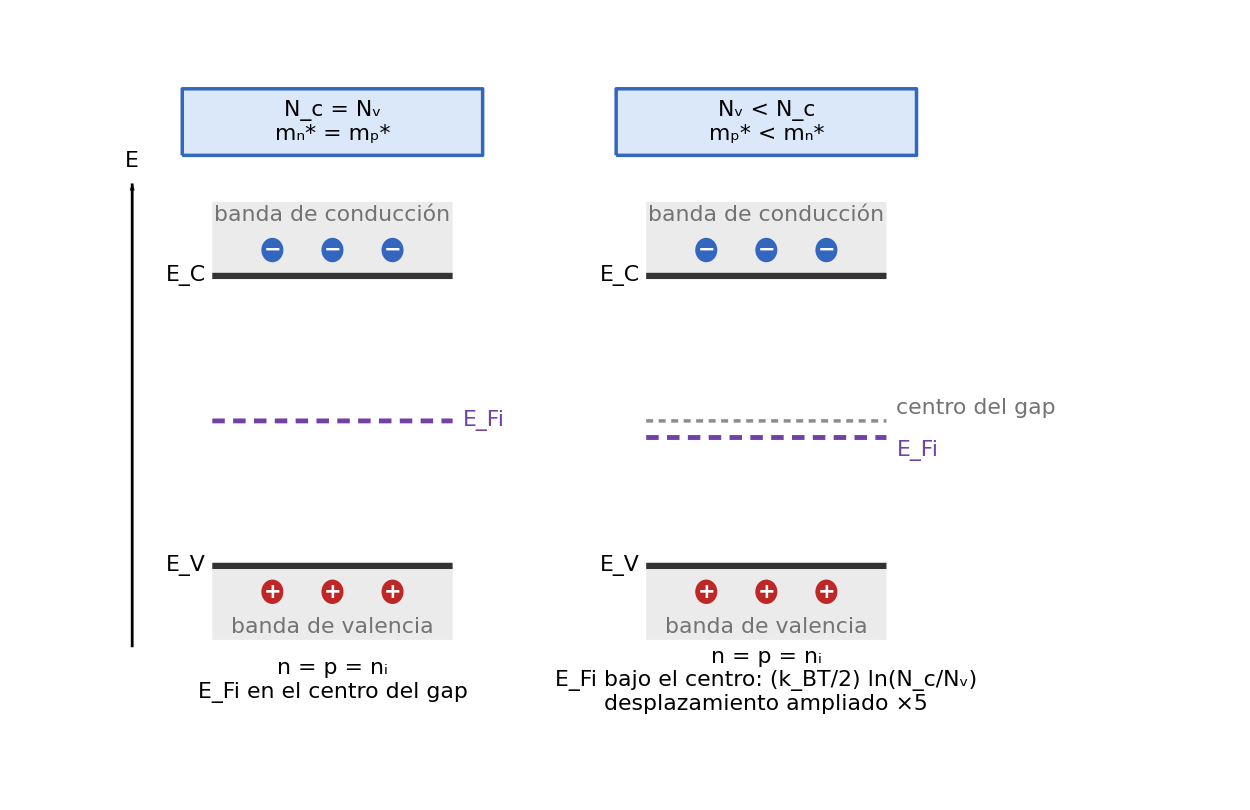

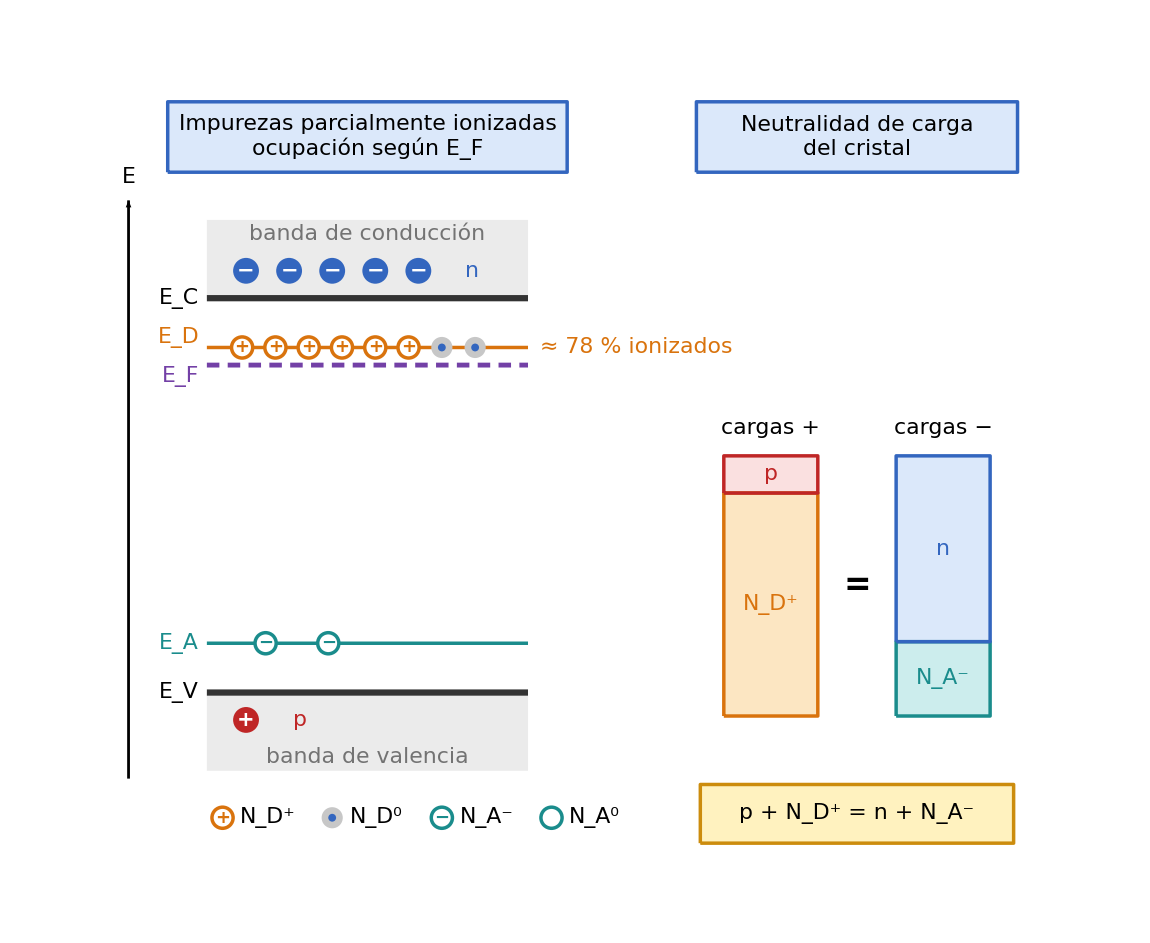

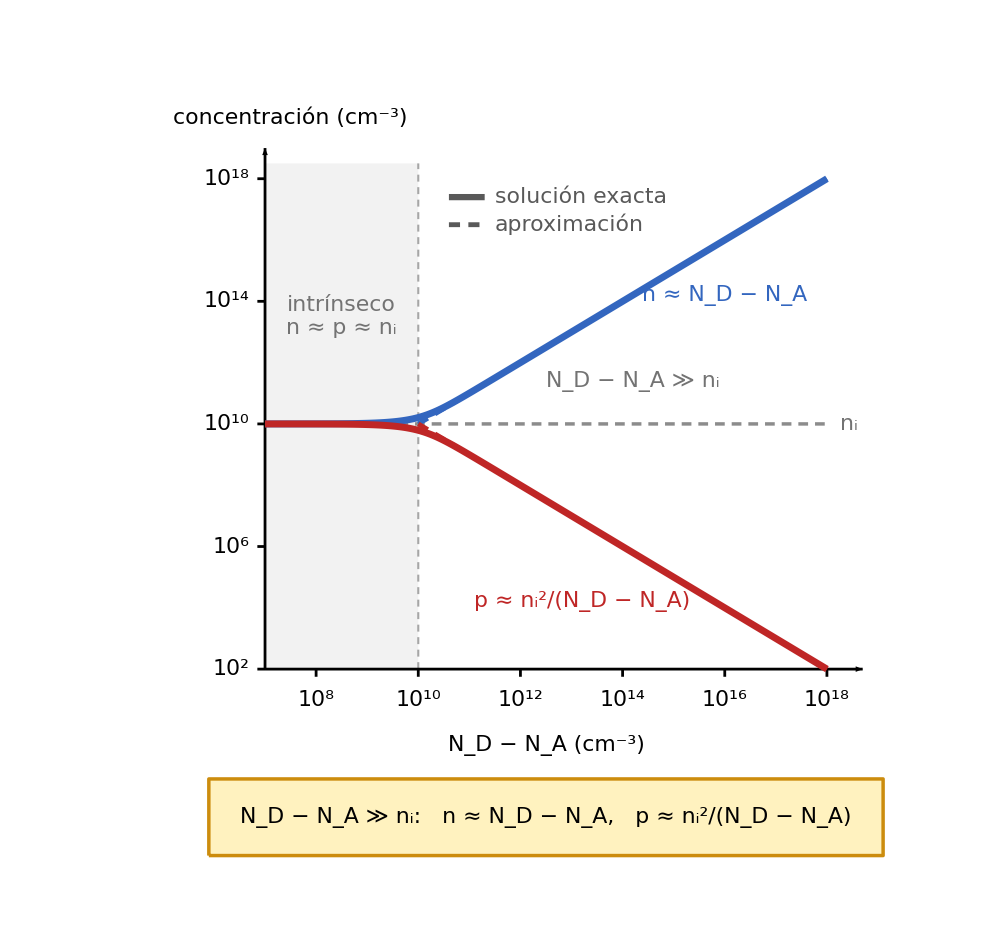

```mathematica
{diagramaIntrinseco,diagramaExtrinseco,diagramaIonizTotal}=Module[{fs,mostrarValores,cAzul,cAzulB,cRojo,cRojoF,cVio,cNar,cTeal,cGris,cOro,cOroB,kT,Eg,ins,insI,insD,caja,carga,ionR,donN,accN,hband,Nc,Nv,amp,shift,se1,yV1,yC1,yM1,yFi1,wb1,pxA,pxB,g1,dD,dA,dFD,gd,ga,NDd,NAd,nHoles,fD,fA,nDion,nAion,nc2,pct,se2,yV2,yC2,yD,yF,yA,px2,wb2,hw,uH,y0b,xb1,xb2,hp,hn,g2,ni,ox,oy,sx3,sy3,XL,YL,curvaN,curvaP,g3},(*----------Parámetros globales----------*)fs=22;(*tamaño de fuente único para todo el gráfico*)mostrarValores=True;(*False oculta el porcentaje de donadores ionizados*)cAzul=RGBColor[0.86,0.91,0.98];cAzulB=RGBColor[0.20,0.40,0.75];
cRojo=RGBColor[0.75,0.15,0.15];cRojoF=RGBColor[0.98,0.88,0.88];
cVio=RGBColor[0.45,0.25,0.65];cNar=RGBColor[0.85,0.45,0.05];
cTeal=RGBColor[0.10,0.55,0.55];cGris=GrayLevel[0.45];
cOro=RGBColor[1.0,0.95,0.75];cOroB=RGBColor[0.80,0.55,0.05];
kT=0.0259;Eg=1.12;
(*----------Funciones auxiliares----------*)ins[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos];
insI[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos,{Left,Center}];
insD[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos,{Right,Center}];
caja[{xc_,yc_},{w_,h_},relleno_,borde_]:={EdgeForm[{AbsoluteThickness[2.5],borde}],relleno,Rectangle[{xc-w/2,yc-h/2},{xc+w/2,yc+h/2},RoundingRadius->0.15]};
carga[pos_,signo_,col_]:={col,Disk[pos,0.33],Text[Style[signo,Round[0.95 fs],Bold,White],pos]};
ionR[pos_,signo_,col_]:={White,Disk[pos,0.27],col,AbsoluteThickness[2.5],Circle[pos,0.27],Text[Style[signo,Round[0.8 fs],Bold,col],pos]};
donN[pos_]:={GrayLevel[0.78],Disk[pos,0.27],cAzulB,Disk[pos,0.1]};
accN[pos_]:={White,Disk[pos,0.27],cTeal,AbsoluteThickness[2.5],Circle[pos,0.27]};
hband[px_,wb_,yv_,yc_]:={{GrayLevel[0.92],EdgeForm[None],Rectangle[{px,yc},{px+wb,yc+2.}],Rectangle[{px,yv-2.},{px+wb,yv}]},{GrayLevel[0.2],AbsoluteThickness[4.5],Line[{{px,yc},{px+wb,yc}}],Line[{{px,yv},{px+wb,yv}}]},ins["banda de conducción",{px+wb/2,yc+1.65},cGris],ins["banda de valencia",{px+wb/2,yv-1.65},cGris],insD[Row[{Subscript["E","C"]}],{px-0.2,yc}],insD[Row[{Subscript["E","V"]}],{px-0.2,yv}]};
(* =====Figura 1:semiconductor intrínseco=====*)Nc=2.8*10.^19;Nv=1.04*10.^19;amp=5.;
shift=amp (kT/2) Log[Nv/Nc];(*desplazamiento de E_Fi (negativo,ampliado)*)se1=7.;yV1=4.6;yC1=yV1+se1 Eg;yM1=(yV1+yC1)/2;yFi1=yM1+se1 shift;
wb1=7.2;pxA=3.4;pxB=16.4;
g1=Graphics[{(*cabeceras*)caja[{pxA+wb1/2,16.6},{9.0,1.8},cAzul,cAzulB],ins[Column[{Row[{Subscript["N","c"]," = ",Subscript["N","v"]}],Row[{Subscript["m","n"],"* = ",Subscript["m","p"],"*"}]},Center],{pxA+wb1/2,16.6}],caja[{pxB+wb1/2,16.6},{9.0,1.8},cAzul,cAzulB],ins[Column[{Row[{Subscript["N","v"]," < ",Subscript["N","c"]}],Row[{Subscript["m","p"],"* < ",Subscript["m","n"],"*"}]},Center],{pxB+wb1/2,16.6}],(*eje de energía y bandas*){Black,AbsoluteThickness[2],Arrowheads[0.018],Arrow[{{1.0,yV1-2.2},{1.0,yC1+2.5}}]},ins[Style["E",Italic],{1.0,yC1+3.1}],hband[pxA,wb1,yV1,yC1],hband[pxB,wb1,yV1,yC1],(*panel izquierdo:E_Fi en el centro del gap*){cVio,AbsoluteThickness[3.5],AbsoluteDashing[{9,6}],Line[{{pxA,yM1},{pxA+wb1,yM1}}]},insI[Row[{Subscript["E","Fi"]}],{pxA+wb1+0.3,yM1},cVio],(*panel derecho:E_Fi por debajo del centro del gap*){GrayLevel[0.55],AbsoluteThickness[2.5],AbsoluteDashing[{5,4}],Line[{{pxB,yM1},{pxB+wb1,yM1}}]},{cVio,AbsoluteThickness[3.5],AbsoluteDashing[{9,6}],Line[{{pxB,yFi1},{pxB+wb1,yFi1}}]},insI["centro del gap",{pxB+wb1+0.3,yM1+0.35},cGris],insI[Row[{Subscript["E","Fi"]}],{pxB+wb1+0.3,yFi1-0.35},cVio],(*n=p en ambos casos*)Table[carga[{pxA+dx,yC1+0.7},"−",cAzulB],{dx,{1.8,3.6,5.4}}],Table[carga[{pxA+dx,yV1-0.7},"+",cRojo],{dx,{1.8,3.6,5.4}}],Table[carga[{pxB+dx,yC1+0.7},"−",cAzulB],{dx,{1.8,3.6,5.4}}],Table[carga[{pxB+dx,yV1-0.7},"+",cRojo],{dx,{1.8,3.6,5.4}}],(*textos inferiores*)ins[Column[{Row[{Style["n",Italic]," = ",Style["p",Italic]," = ",Subscript["n","i"]}],Style[Row[{Subscript["E","Fi"]," en el centro del gap"}],cGris]},Center],{pxA+wb1/2,1.5}],ins[Column[{Row[{Style["n",Italic]," = ",Style["p",Italic]," = ",Subscript["n","i"]}],Style[Row[{Subscript["E","Fi"]," bajo el centro: (",Subscript["k","B"],"T/2) ln(",Subscript["N","c"],"/",Subscript["N","v"],")"}],cGris],Style[Row[{"desplazamiento ampliado ×",Round[amp]}],cGris]},Center],{pxB+wb1/2,1.5}]},ImageSize->1250,PlotRange->{{0.4,28.0},{0.,17.9}},PlotRangePadding->None,AspectRatio->17.9/27.6,Background->White];
(* =====Figura 2:semiconductor extrínseco (ocupación de impurezas y neutralidad)=====*)dD=0.14;dA=0.14;dFD=0.05;gd=2;ga=4;(*E_C-E_D,E_A-E_V,E_D-E_F (eV)*)NDd=8;NAd=2;nHoles=1;(*impurezas y huecos dibujados*)fD=1/(1+gd Exp[-dFD/kT]);(*fracción de donadores ionizados*)fA=1/(1+ga Exp[-(Eg-dD-dFD-dA)/kT]);(*fracción de aceptadores ionizados*)nDion=Round[NDd fD];nAion=Round[NAd fA];
nc2=Max[nDion-nAion+nHoles,0];(*electrones libres:neutralidad*)pct=Round[100 fD];
se2=9.;yV2=4.4;yC2=yV2+se2 Eg;
yD=yC2-se2 dD;yF=yD-se2 dFD;yA=yV2+se2 dA;
px2=3.0;wb2=8.2;
hw=1.2;uH=0.95;y0b=3.8;xb1=17.4;xb2=21.8;
hp=(nHoles+nDion) uH;hn=(nc2+nAion) uH;
g2=Graphics[{(*cabeceras*)caja[{px2+wb2/2,18.6},{10.2,1.8},cAzul,cAzulB],ins[Column[{"Impurezas parcialmente ionizadas",Row[{"ocupación según ",Subscript["E","F"]}]},Center],{px2+wb2/2,18.6}],caja[{19.6,18.6},{8.2,1.8},cAzul,cAzulB],ins[Column[{"Neutralidad de carga","del cristal"},Center],{19.6,18.6}],(*eje de energía,bandas y niveles*){Black,AbsoluteThickness[2],Arrowheads[0.018],Arrow[{{1.0,yV2-2.2},{1.0,yC2+2.5}}]},ins[Style["E",Italic],{1.0,yC2+3.1}],hband[px2,wb2,yV2,yC2],{cNar,AbsoluteThickness[2.5],Line[{{px2,yD},{px2+wb2,yD}}]},{cVio,AbsoluteThickness[3.5],AbsoluteDashing[{9,6}],Line[{{px2,yF},{px2+wb2,yF}}]},{cTeal,AbsoluteThickness[2.5],Line[{{px2,yA},{px2+wb2,yA}}]},insD[Row[{Subscript["E","D"]}],{px2-0.2,yD+0.25},cNar],insD[Row[{Subscript["E","F"]}],{px2-0.2,yF-0.3},cVio],insD[Row[{Subscript["E","A"]}],{px2-0.2,yA},cTeal],(*donadores (ionizados con aro+,neutros con su electrón) y aceptadores*)Table[If[k<nDion,ionR[{px2+0.9+0.85 k,yD},"+",cNar],donN[{px2+0.9+0.85 k,yD}]],{k,0,NDd-1}],Table[If[k<nAion,ionR[{px2+1.5+1.6 k,yA},"−",cTeal],accN[{px2+1.5+1.6 k,yA}]],{k,0,NAd-1}],If[mostrarValores,insI[Row[{"≈ ",pct," % ionizados"}],{px2+wb2+0.3,yD},cNar],{}],(*portadores libres*)Table[carga[{px2+1.0+1.1 i,yC2+0.7},"−",cAzulB],{i,0,nc2-1}],insI[Style["n",Italic],{px2+1.0+1.1 nc2+0.1,yC2+0.7},cAzulB],Table[carga[{px2+1.0+1.1 i,yV2-0.7},"+",cRojo],{i,0,nHoles-1}],insI[Style["p",Italic],{px2+1.0+1.1 nHoles+0.1,yV2-0.7},cRojo],(*leyenda*)ionR[{3.4,1.2},"+",cNar],insI[Row[{Subsuperscript["N","D","+"]}],{3.85,1.2}],donN[{6.2,1.2}],insI[Row[{Subsuperscript["N","D","0"]}],{6.65,1.2}],ionR[{9.0,1.2},"−",cTeal],insI[Row[{Subsuperscript["N","A","−"]}],{9.45,1.2}],accN[{11.8,1.2}],insI[Row[{Subsuperscript["N","A","0"]}],{12.25,1.2}],(*barras de carga:positivas (p+N_D+) y negativas (n+N_A-)*){EdgeForm[{AbsoluteThickness[2.5],cNar}],RGBColor[0.99,0.90,0.76],Rectangle[{xb1-hw,y0b},{xb1+hw,y0b+nDion uH}]},{EdgeForm[{AbsoluteThickness[2.5],cRojo}],cRojoF,Rectangle[{xb1-hw,y0b+nDion uH},{xb1+hw,y0b+hp}]},{EdgeForm[{AbsoluteThickness[2.5],cTeal}],RGBColor[0.80,0.93,0.93],Rectangle[{xb2-hw,y0b},{xb2+hw,y0b+nAion uH}]},{EdgeForm[{AbsoluteThickness[2.5],cAzulB}],cAzul,Rectangle[{xb2-hw,y0b+nAion uH},{xb2+hw,y0b+hn}]},ins[Row[{Subsuperscript["N","D","+"]}],{xb1,y0b+nDion uH/2},cNar],ins[Style["p",Italic],{xb1,y0b+nDion uH+nHoles uH/2},cRojo],ins[Row[{Subsuperscript["N","A","−"]}],{xb2,y0b+nAion uH/2},cTeal],ins[Style["n",Italic],{xb2,y0b+nAion uH+nc2 uH/2},cAzulB],ins["cargas +",{xb1,y0b+hp+0.7}],ins["cargas −",{xb2,y0b+hn+0.7}],Text[Style["=",Round[1.5 fs],Bold],{(xb1+xb2)/2,y0b+hp/2}],caja[{19.6,1.3},{8.0,1.5},cOro,cOroB],ins[Row[{Style["p",Italic]," + ",Subsuperscript["N","D","+"]," = ",Style["n",Italic]," + ",Subsuperscript["N","A","−"]}],{19.6,1.3}]},ImageSize->1150,PlotRange->{{0.4,24.4},{0.2,19.9}},PlotRangePadding->None,AspectRatio->19.7/24.0,Background->White];
(* =====Figura 3:ionización total,solución de la cuadrática=====*)ni=1.*10.^10;
ox=4.2;oy=3.6;sx3=1.0;sy3=0.6;
XL[l_]:=ox+sx3 (l-7);(*l=log10(N_D-N_A)*)YL[l_]:=oy+sy3 (l-2);(*l=log10(concentración)*)curvaN=Table[With[{x=10.^l},{XL[l],YL[Log10[x/2+Sqrt[x^2/4+ni^2]]]}],{l,7.,18.,0.05}];
curvaP=Table[With[{x=10.^l},{XL[l],YL[Log10[ni^2/(x/2+Sqrt[x^2/4+ni^2])]]}],{l,7.,18.,0.05}];
g3=Graphics[{(*zona intrínseca*){GrayLevel[0.95],EdgeForm[None],Rectangle[{XL[7],oy},{XL[10],YL[18]+0.3}]},{GrayLevel[0.65],AbsoluteThickness[1.5],AbsoluteDashing[{5,4}],Line[{{XL[10],oy},{XL[10],YL[18]+0.3}}]},(*ejes*){Black,AbsoluteThickness[2],Arrowheads[0.02],Arrow[{{ox,oy},{XL[18]+0.7,oy}}],Arrow[{{ox,oy},{ox,YL[18]+0.6}}]},Table[{Black,AbsoluteThickness[2],Line[{{XL[k],oy},{XL[k],oy-0.15}}],ins[Row[{Superscript["10",k]}],{XL[k],oy-0.6}]},{k,8,18,2}],Table[{Black,AbsoluteThickness[2],Line[{{ox-0.15,YL[k]},{ox,YL[k]}}],insD[Row[{Superscript["10",k]}],{ox-0.3,YL[k]}]},{k,2,18,4}],ins[Row[{Subscript["N","D"]," − ",Subscript["N","A"]," (",Superscript["cm","−3"],")"}],{XL[12.5],oy-1.5}],insI[Row[{"concentración (",Superscript["cm","−3"],")"}],{ox-1.8,YL[18]+1.2}],(*n_i*){GrayLevel[0.55],AbsoluteThickness[2.5],AbsoluteDashing[{7,5}],Line[{{XL[7],YL[10]},{XL[18],YL[10]}}]},insI[Row[{Subscript["n","i"]}],{XL[18]+0.25,YL[10]},cGris],(*aproximaciones (discontinuas) y solución exacta (continua)*){cAzulB,AbsoluteThickness[3.5],AbsoluteDashing[{8,6}],Line[{{XL[10],YL[10]},{XL[18],YL[18]}}]},{cRojo,AbsoluteThickness[3.5],AbsoluteDashing[{8,6}],Line[{{XL[10],YL[10]},{XL[18],YL[2]}}]},{cAzulB,AbsoluteThickness[5],Line[curvaN]},{cRojo,AbsoluteThickness[5],Line[curvaP]},(*etiquetas*)ins[Column[{"intrínseco",Row[{Style["n",Italic]," ≈ ",Style["p",Italic]," ≈ ",Subscript["n","i"]}]},Center],{XL[8.5],YL[13.5]},cGris],ins[Row[{Subscript["N","D"]," − ",Subscript["N","A"]," ≫ ",Subscript["n","i"]}],{XL[14.2],YL[11.4]},cGris],ins[Row[{Style["n",Italic]," ≈ ",Subscript["N","D"]," − ",Subscript["N","A"]}],{XL[16.0],YL[14.2]},cAzulB],ins[Row[{Style["p",Italic]," ≈ ",Subsuperscript["n","i",2],"/(",Subscript["N","D"]," − ",Subscript["N","A"],")"}],{XL[13.2],YL[4.2]},cRojo],(*leyenda*){GrayLevel[0.35],AbsoluteThickness[4.5],Line[{{XL[10.6],YL[17.4]},{XL[11.3],YL[17.4]}}]},insI["solución exacta",{XL[11.5],YL[17.4]},GrayLevel[0.35]],{GrayLevel[0.35],AbsoluteThickness[3.5],AbsoluteDashing[{8,6}],Line[{{XL[10.6],YL[16.5]},{XL[11.3],YL[16.5]}}]},insI["aproximación",{XL[11.5],YL[16.5]},GrayLevel[0.35]],(*resultado*)caja[{XL[12.5],0.7},{13.2,1.5},cOro,cOroB],ins[Row[{Subscript["N","D"]," − ",Subscript["N","A"]," ≫ ",Subscript["n","i"],":   ",Style["n",Italic]," ≈ ",Subscript["N","D"]," − ",Subscript["N","A"],",   ",Style["p",Italic]," ≈ ",Subsuperscript["n","i",2],"/(",Subscript["N","D"]," − ",Subscript["N","A"],")"}],{XL[12.5],0.7}]},ImageSize->1000,PlotRange->{{0.8,16.8},{-0.2,15.0}},PlotRangePadding->None,AspectRatio->15.2/16.0,Background->White];
{g1,g2,g3}];
diagramaIntrinseco
diagramaExtrinseco
diagramaIonizTotal
```

```mathematica
Export["T2_4_intrinseco.png",diagramaIntrinseco,Background->None,ImageResolution->300,ImageSize->1250]
Export["T2_4_extrinseco.png",diagramaExtrinseco,Background->None,ImageResolution->300,ImageSize->1150]
Export["T2_4_ioniz_total.png",diagramaIonizTotal,Background->None,ImageResolution->300,ImageSize->1000]
```

T2_4_intrinseco.png

T2_4_extrinseco.png

T2_4_ioniz_total.png

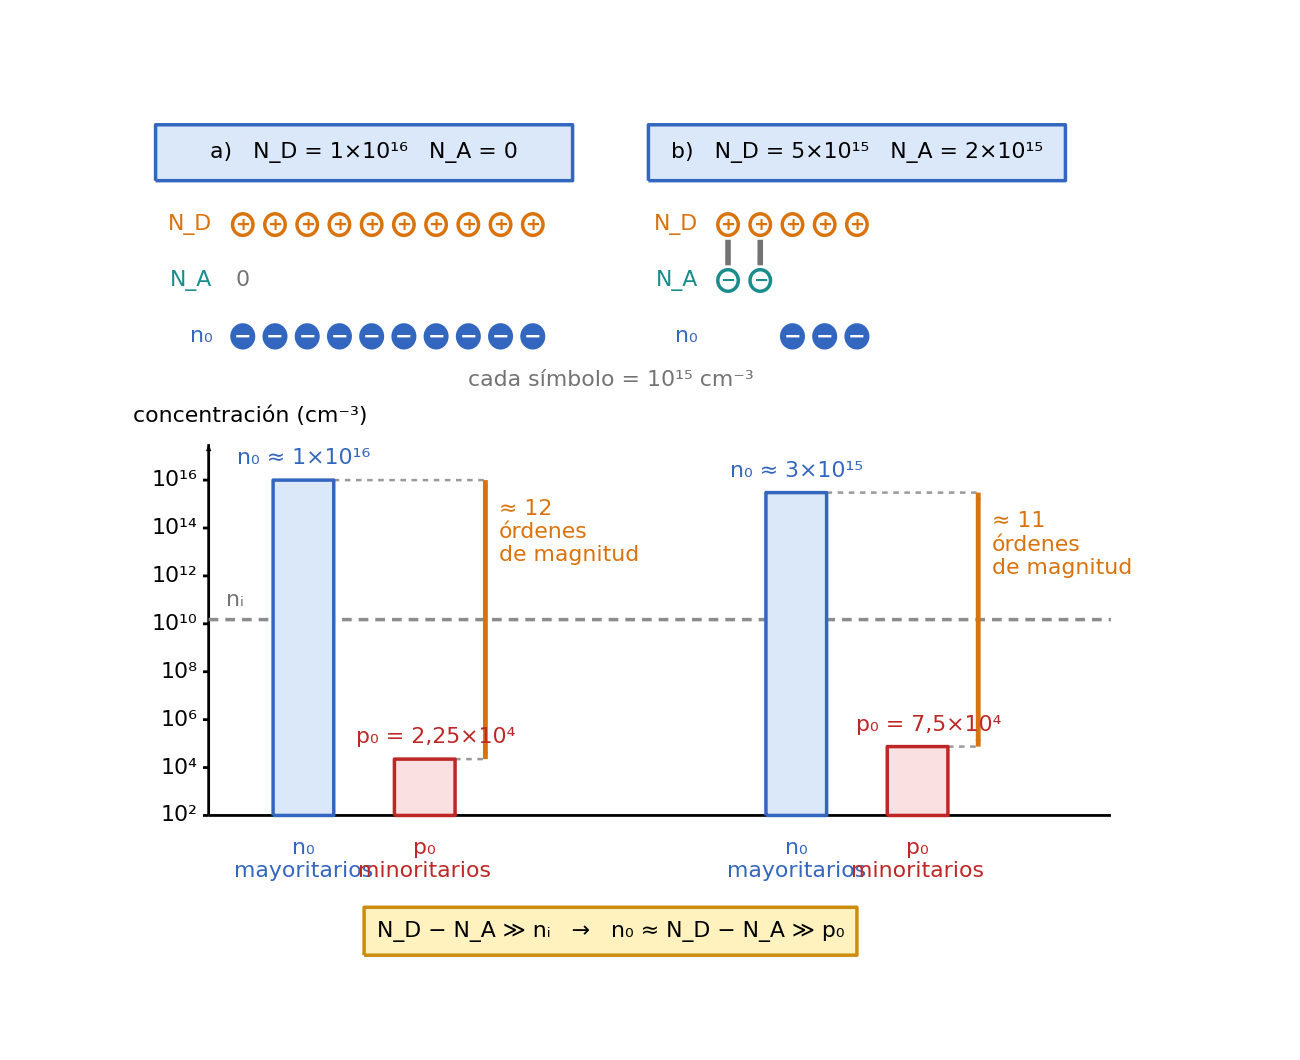

```mathematica
diagramaSiDopado=Module[{fs,mostrarValores,cAzul,cAzulB,cRojo,cRojoF,cNar,cTeal,cGris,cOro,cOroB,ni,ud,y0c,sc,xax,cxa,cxb,yl,ins,insI,insD,flecha,caja,carga,ionR,cient,grupo},(*----------Parámetros globales----------*)fs=22;(*tamaño de fuente único para todo el gráfico*)mostrarValores=True;(*False oculta los valores calculados de n0,p0 y los órdenes de magnitud*)cAzul=RGBColor[0.86,0.91,0.98];cAzulB=RGBColor[0.20,0.40,0.75];
cRojo=RGBColor[0.75,0.15,0.15];cRojoF=RGBColor[0.98,0.88,0.88];
cNar=RGBColor[0.85,0.45,0.05];cTeal=RGBColor[0.10,0.55,0.55];
cGris=GrayLevel[0.45];
cOro=RGBColor[1.0,0.95,0.75];cOroB=RGBColor[0.80,0.55,0.05];
(*----------Datos del ejemplo (cm^-3)----------*)ni=1.5*10.^10;ud=10.^15;(*n_i y valor de cada símbolo del pictograma*)(*----------Geometría----------*)y0c=3.0;sc=0.6;(*base del gráfico logarítmico y altura por década*)xax=2.4;cxa=6.5;cxb=19.5;(*eje vertical y centro de cada columna*)yl[c_]:=y0c+sc (Log10[c]-2);
(*----------Funciones auxiliares----------*)ins[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos];
insI[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos,{Left,Center}];
insD[expr_,pos_,col_:Black]:=Inset[Style[expr,fs,col],pos,{Right,Center}];
flecha[p1_,p2_,col_,s_:0.02]:={col,AbsoluteThickness[4],Arrowheads[s],Arrow[{p1,p2}]};
caja[{xc_,yc_},{w_,h_},relleno_,borde_]:={EdgeForm[{AbsoluteThickness[2.5],borde}],relleno,Rectangle[{xc-w/2,yc-h/2},{xc+w/2,yc+h/2},RoundingRadius->0.15]};
carga[pos_,signo_,col_]:={col,Disk[pos,0.33],Text[Style[signo,Round[0.95 fs],Bold,White],pos]};
ionR[pos_,signo_,col_]:={White,Disk[pos,0.27],col,AbsoluteThickness[2.5],Circle[pos,0.27],Text[Style[signo,Round[0.8 fs],Bold,col],pos]};
cient[x_]:=Module[{ex=Floor[Log10[x]],m,txt},m=Round[x/10.^ex,0.01];
txt=Which[Abs[m-Round[m]]<10^-6,Round[m],Abs[m-Round[m,0.1]]<10^-6,NumberForm[m,{2,1},NumberPoint->","],True,NumberForm[m,{3,2},NumberPoint->","]];
Row[{txt,"×",Superscript["10",ex]}]];
(*----------Una columna:pictograma de dopado y barras de n0 y p0----------*)grupo[cx_,xs0_,xl_,NDv_,NAv_,letra_]:=Module[{nDc,nAc,nEc,nn,pp,xn,xp,yD,yA,yE,dx},nDc=Round[NDv/ud];nAc=Round[NAv/ud];nEc=nDc-nAc;
nn=(NDv-NAv)/2+Sqrt[((NDv-NAv)/2)^2+ni^2];(*solución de la cuadrática*)pp=ni^2/nn;(*ley de acción de masas*)xn=cx-1.6;xp=cx+1.6;
{yD,yA,yE}={17.8,16.4,15.0};dx=0.85;
{(*cabecera*)caja[{cx,19.6},{11.0,1.4},cAzul,cAzulB],ins[Row[{Style[letra,Bold],")   ",Subscript["N","D"]," = ",cient[NDv],"   ",Subscript["N","A"]," = ",If[NAv==0,"0",cient[NAv]]}],{cx,19.6}],(*pictograma:donadores,aceptadores y electrones libres*)insD[Row[{Subscript["N","D"]}],{xl,yD},cNar],insD[Row[{Subscript["N","A"]}],{xl,yA},cTeal],insD[Row[{Subscript["n","0"]}],{xl,yE},cAzulB],Table[ionR[{xs0+dx i,yD},"+",cNar],{i,0,nDc-1}],Table[ionR[{xs0+dx i,yA},"−",cTeal],{i,0,nAc-1}],If[nAc==0,ins["0",{xs0,yA},cGris],{}],Table[flecha[{xs0+dx i,yD-0.38},{xs0+dx i,yA+0.38},cGris,0.012],{i,0,nAc-1}],Table[carga[{xs0+dx (nAc+i),yE},"−",cAzulB],{i,0,nEc-1}],(*barras de concentración*){EdgeForm[{AbsoluteThickness[2.5],cAzulB}],cAzul,Rectangle[{xn-0.8,y0c},{xn+0.8,yl[nn]}]},{EdgeForm[{AbsoluteThickness[2.5],cRojo}],cRojoF,Rectangle[{xp-0.8,y0c},{xp+0.8,yl[pp]}]},ins[Row[{Subscript["n","0"],If[mostrarValores,Row[{" ≈ ",cient[nn]}],""]}],{xn,yl[nn]+0.55},cAzulB],ins[Row[{Subscript["p","0"],If[mostrarValores,Row[{" = ",cient[pp]}],""]}],{xp+0.3,yl[pp]+0.55},cRojo],ins[Column[{Row[{Subscript["n","0"]}],"mayoritarios"},Center],{xn,1.9},cAzulB],ins[Column[{Row[{Subscript["p","0"]}],"minoritarios"},Center],{xp,1.9},cRojo],(*distancia entre mayoritarios y minoritarios*){GrayLevel[0.6],AbsoluteThickness[1.8],AbsoluteDashing[{4,4}],Line[{{xn+0.8,yl[nn]},{cx+3.2,yl[nn]}}],Line[{{xp+0.8,yl[pp]},{cx+3.2,yl[pp]}}]},{cNar,AbsoluteThickness[3.5],Arrowheads[{-0.014,0.014}],Arrow[{{cx+3.2,yl[pp]},{cx+3.2,yl[nn]}}]},insI[Column[{If[mostrarValores,Row[{"≈ ",Round[Log10[nn/pp]]}],""],"órdenes","de magnitud"},Left],{cx+3.55,yl[nn]-1.3},cNar]}];
(*----------Diagrama----------*)Graphics[{(*ejes del gráfico logarítmico y densidad intrínseca*){Black,AbsoluteThickness[2],Arrowheads[0.018],Arrow[{{xax,y0c},{xax,12.3}}]},{Black,AbsoluteThickness[2],Line[{{xax,y0c},{26.2,y0c}}]},insI[Row[{"concentración (",Superscript["cm","−3"],")"}],{0.4,13.0}],Table[{Black,AbsoluteThickness[2],Line[{{xax-0.15,yl[10.^k]},{xax,yl[10.^k]}}],insD[Row[{Superscript["10",k]}],{xax-0.3,yl[10.^k]}]},{k,2,16,2}],{GrayLevel[0.55],AbsoluteThickness[2.5],AbsoluteDashing[{7,5}],Line[{{xax,yl[ni]},{26.2,yl[ni]}}]},ins[Row[{Subscript["n","i"]}],{xax+0.7,yl[ni]+0.5},cGris],(*casos a) y b)*)grupo[cxa,3.3,2.5,1.*10.^16,0.,"a"],grupo[cxb,16.1,15.3,5.*10.^15,2.*10.^15,"b"],ins[Row[{"cada símbolo = ",Superscript["10",15]," ",Superscript["cm","−3"]}],{13.0,13.9},cGris],(*conclusión*)caja[{13.0,0.1},{13.0,1.2},cOro,cOroB],ins[Row[{Subscript["N","D"]," − ",Subscript["N","A"]," ≫ ",Subscript["n","i"],"   →   ",Subscript["n","0"]," ≈ ",Subscript["N","D"]," − ",Subscript["N","A"]," ≫ ",Subscript["p","0"]}],{13.0,0.1}]},ImageSize->1300,PlotRange->{{0,26.6},{-0.7,21.0}},PlotRangePadding->None,AspectRatio->21.7/26.6,Background->White]];
diagramaSiDopado
```

```mathematica
Export["T2_E3.png",diagramaSiDopado,Background->None,ImageResolution->300,ImageSize->1300]
```

T2_E3.png